## Operations on Lists

There are thousands of functions in the Wolfram Language that work with lists.

You can do arithmetic with lists:

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
{1,1,2}*{1,2,3}
```

{1,2,6}

Compute the first 10 squares:

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

Plot the first 20 squares:

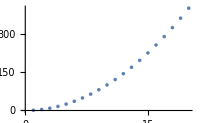

```mathematica
ListPlot[Range[20]^2]
```

Sort sorts a list into order:

```mathematica
Sort[{4,2,1,3,6}]
```

{1,2,3,4,6}

Length finds how long a list is:

```mathematica
Length[{5,3,4,5,3,4,5}]
```

7

Total gives the total from adding up a list:

```mathematica
Total[{1,1,2,2}]
```

6

Find the total of the numbers from 1 to 10:

```mathematica
Total[Range[10]]
```

55

Count counts the number of times something appears in a list.

Count the number of times a appears in the list:

```mathematica
Count[{a,b,a,a,c,b,a},a]
```

4

It’s often useful to be able to get individual elements of a list. First gives the first element; Last gives the last element. Part gives the element at a particular position.

Pick out the first element of a list:

```mathematica
First[{7,6,5}]
```

7

Pick out the last element:

```mathematica
Last[{7,6,5}]
```

5

Pick out element number 2:

```mathematica
Part[{7,6,5},2]
```

6

Picking out the first element in a list you’ve sorted is the same as finding the minimum element:

```mathematica
First[Sort[{6,7,1,2,4,5}]]
```

1

```mathematica
Min[{6,7,1,2,4,5}]
```

1

If you have a number, like 5671, you can make a list of its digits using IntegerDigits[5671].

Break a number into a list of digits:

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

Find the last digit:

```mathematica
Last[IntegerDigits[1988]]
```

8

Take lets you take a specified number of elements from the beginning of a list.

Take the first 3 elements from a list:

```mathematica
Take[{101,203,401,602,332,412},3]
```

{101,203,401}

Take the first 10 digits of 2 to the power 100:

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

Drop drops elements from the beginning of a list.

```mathematica
Drop[{101,203,401,602,332,412},3]
```

{602,332,412}

Vocabulary

{2,3,4}+{5,6,2} |   | arithmetic on lists 
Sort[{5,7,1}] |   | sort a list into order 
Length[{3,3}] |   | length of a list (number of elements) 
Total[{1,1,2}] |   | total of all elements in a list 
Count[{3,2,3},3] |   | count occurrences of an element
First[{2,3}] |   | first element in a list 
Last[{6,7,8}] |   | last element in a list 
Part[{3,1,4},2] |   | particular part of a list, also written as {3,1,4}[[2]]
Take[{6,4,3,1},2] |   | take elements from the beginning of a list 
Drop[{6,4,3,1},2] |   | drop elements from the beginning of a list
IntegerDigits[1234] |   | list of digits in a number

"14 Exercises Available"
"with 7 extras" | "Get Started »"

Make a list of the first 10 squares, in reverse order. »

| Expected output: |  
  | {100,81,64,49,36,25,16,9,4,1} |

Find the total of the first 10 squares. »

| Expected output: |  
  | 385 |

Make a plot of the first 10 squares, starting at 1. »

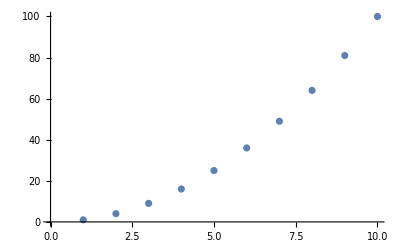
| Expected output: |  
  | -Graphics- |

Use Sort, Join and Range to create {1,1,2,2,3,3,4,4}. »

| Expected output: |  
  | {1,1,2,2,3,3,4,4} |

Use Range and + to make a list of numbers from 10 to 20, inclusive. »

| Expected output: |  
  | {10,11,12,13,14,15,16,17,18,19,20} |

Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order. »

| Expected output: |  
  | {1,1,4,8,9,16,25,27,64,125} |

Find the number of digits in 2^128. »

| Expected output: |  
  | 39 |

Find the first digit of 2^32. »

| Expected output: |  
  | 4 |

Find the first 10 digits in 2^100. »

| Expected output: |  
  | {1,2,6,7,6,5,0,6,0,0} |

Find the largest digit that appears in 2^20. »

| Expected output: |  
  | 8 |

Find how many zeros appear in the digits of 2^1000. »

| Expected output: |  
  | 28 |

Use Part, Sort and IntegerDigits to find the second-smallest digit in 2^20. »

| Expected output: |  
  | 1 |

Make a line plot of the sequence of digits that appear in 2^128. »

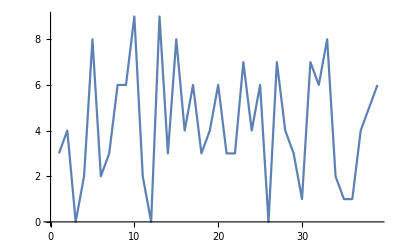
| Expected output: |  
  | -Graphics- |

Use Take and Drop to get the sequence 11 through 20 from Range[100]. »

| Expected output: |  
  | {11,12,13,14,15,16,17,18,19,20} |

Make a list of the first 10 multiples of 3. »

| Expected output: |  
  | {3,6,9,12,15,18,21,24,27,30} |

Make a list of the first 10 squares using only Range and Times. »

| Expected output: |  
  | {1,4,9,16,25,36,49,64,81,100} |

Find the last digit of 2^37. »

| Expected output: |  
  | 2 |

Find the second-to-last digit of 2^32. »

| Expected output: |  
  | 9 |

Find the sum of all the digits of 3^126. »

| Expected output: |  
  | 234 |

Make a pie chart of the sequence of digits that appear in 2^32. »

| Expected output: |  
  | -Graphics- |

Make a list of pie charts for the sequence of digits in 2^20, 2^40, 2^60. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Q&A

Can one add lists of different lengths?

No. {1,2}+{1,2,3} won’t work. {1,2,0}+{1,2,3} would be fine, if that’s what you mean.

Can there be a list with nothing in it?

Yes. {} is a list of length 0, with no elements. It’s usually called the null list or the empty list.

Tech Notes

IntegerDigits[5671] gives digits in base 10. IntegerDigits[5671,2] gives digits in base 2. You can use any base you want. FromDigits[{5,6,7,1}] reconstructs a number from its list of digits.

Rest[list] gives all the elements of list after the first one. Most[list] gives all elements other than the last one.

More to Explore

Guide to List Manipulation in the Wolfram Language »